```mathematica
<<FiniteFlow`
```

```mathematica
A = {{3a,6,7,b,3+b},{11,4,2b,32,11+c},{1,3,23,a+b/a,1/(d+a)},{2,a^2+b,1/(a+b+c),d,1/d^2},{3+a,32,a/c,17/d,1}};
```

```mathematica
(*n = A // Length;
c[n]=1;
M[0]=ConstantArray[0,{n,n}];
For[k=1,k<=n,k++,
M[k]=A.M[k-1]+c[n-k+1]*IdentityMatrix[n];
c[n-k]=-1/k Tr[A.M[k]];
];
coeff2=Array[c,3+1,0] // Factor*)
```

```mathematica
(*------run------*)
```

```mathematica
(*Faddeev–LeVerrier algorithm in FiniteFlow*)
```

```mathematica
Unique[]
```

$11

```mathematica
params = A // Variables;
n = A // Length;
Clear[{c,M,J,AM,cptsAM,trAM,numprefactor}]
traceTakePattern = Table[1+i*n+i,{i,0,n-1}] // {{1},#}&//Tuples;
diagMat = dvar*IdentityMatrix[n]//Flatten;
sumPatternVars = Array[dvars,n];
sumPattern = sumPatternVars // Apply[Plus];
```

```mathematica
FFNewGraph["characteristicPolynomial","in",params];
FFAlgRatExprEval["characteristicPolynomial","A",{"in"},params,A//Flatten];
FFAlgRatFunEval["characteristicPolynomial",c[n+1]//ToString,{"in"},params,{0}];
FFAlgRatFunEval["characteristicPolynomial",c[n]//ToString,{"in"},params,{1}];
FFAlgRatFunEval["characteristicPolynomial",J[n]//ToString,{c[n]//ToString},{dvar},diagMat];
(*FFAlgRatFunEval["characteristicPolynomial",M[0]//ToString,{c[n+1]//ToString},{dvar},diagMat];*)
FFAlgRatFunEval["characteristicPolynomial",AM[0]//ToString,{c[n+1]//ToString},{dvar},diagMat];
```

```mathematica
Do[
FFAlgAdd["characteristicPolynomial",M[k]//ToString,{AM[k-1]//ToString,J[n-k+1]//ToString}];
FFAlgMatMul["characteristicPolynomial",AM[k]//ToString,{"A",M[k]//ToString},n,n,n];

FFAlgTake["characteristicPolynomial",cptsAM[k]//ToString,{AM[k]//ToString},traceTakePattern];
FFAlgRatFunEval["characteristicPolynomial",trAM[k]//ToString,{cptsAM[k]//ToString},sumPatternVars,{sumPattern}];

FFAlgRatFunEval["characteristicPolynomial",numprefactor[k]//ToString,{"in"},params,{-1/k}];
FFAlgMul["characteristicPolynomial",c[n-k]//ToString,{numprefactor[k]//ToString,trAM[k]//ToString}];
FFAlgRatFunEval["characteristicPolynomial",J[n-k]//ToString,{c[n-k]//ToString},{dvar},diagMat];
,
{k,n}
];//AbsoluteTiming
```

{0.00236,Null}

```mathematica
FFAlgTake["characteristicPolynomial","out",Array[c,n+1,0]//Map[ToString],Range[n+1]//{#,{1}}&//Tuples]
```

True

```mathematica
FFGraphOutput["characteristicPolynomial","out"]
rec=FFReconstructFunction["characteristicPolynomial",params,"PrintDebugInfo"->1]; // AbsoluteTiming
```

Generated 1096 sample points

Approximate time per evaluation (single core): 3.1e-05 sec.

{0.015134,Null}

```mathematica
char=CharacteristicPolynomial[A,λ]//CoefficientList[#,λ]&;//AbsoluteTiming
```

{0.0123,Null}

```mathematica
rec/char//Factor
```

{-1,-1,-1,-1,-1,-1}

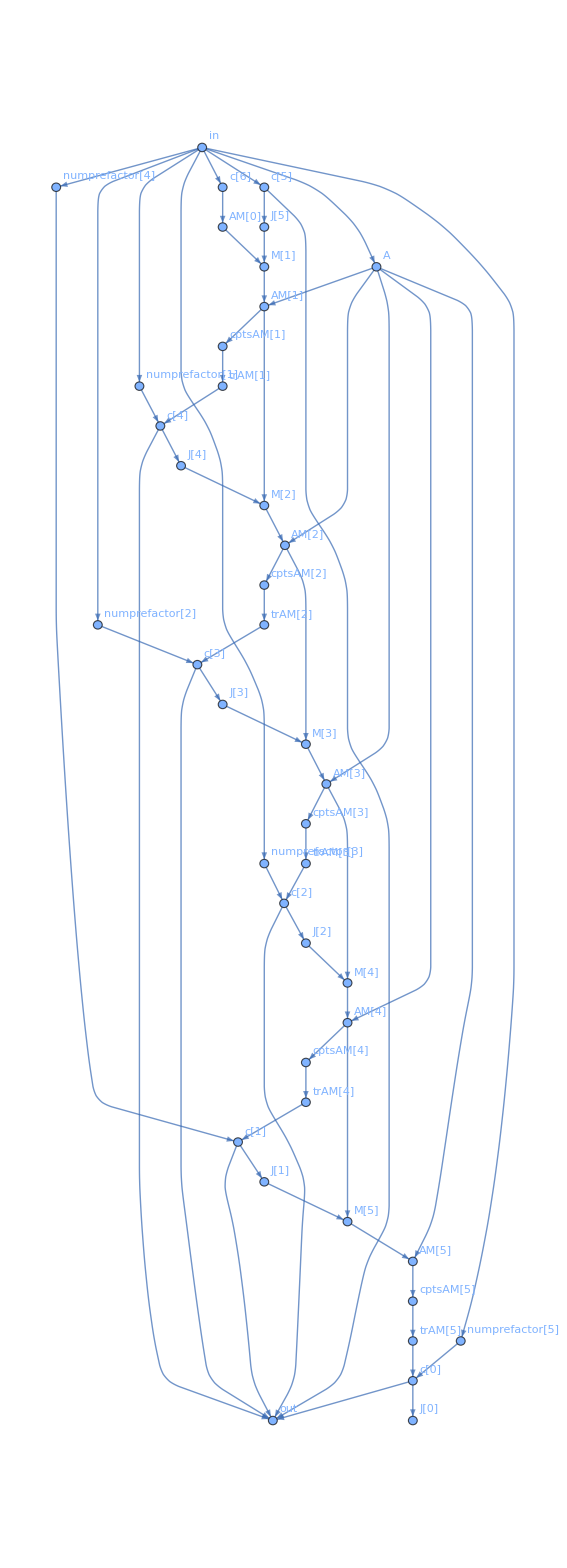

```mathematica
"characteristicPolynomial"//FFGraphDraw
```